32

{-32,-31,-30,-29,-28,-27,-26,-25,-24,-23,-22,-21,-20,-19,-18,-17,-16,-15,-14,-13,-12,-11,-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32}

Throw::nocatch: Uncaught Throw[Il numero è al di fuori dell'intervallo consentito.] returned to top level.

Hold[Throw[Il numero è al di fuori dell'intervallo consentito.]]

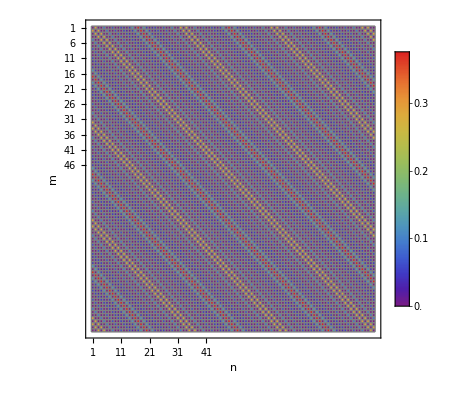

done

```mathematica
(*Funzione per generare gli array theta e phi*)generateArray[n_]:=Module[{start,end,thetaVec,phiVec},start=-(2^(n/2-1));
end=2^(n/2-1);
thetaVec=Table[i+0.5,{i,start,end-1}];
phiVec=thetaVec;(*phiVec è uguale a thetaVec in questo caso*){thetaVec,phiVec}]

(*Funzione per convertire double in stringa binaria*)
doubleToString[number_,n_]:=Module[{lowerBound,upperBound,offsetNumber,binaryString},If[!NumberQ[number],Throw["number deve essere un float o un int"]];
lowerBound=-(2^(n/2-1))+0.5;
upperBound=2^(n/2-1)-0.5;
If[number<lowerBound||number>upperBound,Throw["Il numero è al di fuori dell'intervallo consentito."]];
offsetNumber=number-lowerBound;
binaryString=IntegerString[Floor[offsetNumber],2,32];
StringTake[binaryString,-(n/2)]]

(*Funzione per convertire stringa binaria in double*)
stringToDouble[binaryStr_]:=Module[{offset},offset=FromDigits[binaryStr,2];
offset-2^(StringLength[binaryStr]-1)+0.5]

(*Funzione per emulare l'operatore Z1Z2*)
ZOp[phi_,nQubs_]:=Module[{binStr},binStr=doubleToString[phi,nQubs];
If[StringTake[binStr,2]=="00"||StringTake[binStr,2]=="11",1,-1]]

(*Funzione per emulare l'operatore X1X2*)
XOp[phi_,nQubs_]:=Module[{binStr,modBinStr,newPhi},binStr=doubleToString[phi,nQubs];
modBinStr=StringJoin[If[StringTake[binStr,1]=="0","1","0"],If[StringTake[StringDrop[binStr,1],1]=="0","1","0"],StringDrop[binStr,2]];
newPhi=stringToDouble[modBinStr];
newPhi]

(*Funzione per l'integrale della componente phi*)
integralPhi[phi_,m_,n_,op_,nQubs_]:=Module[{result=0.0,deltaPhi,Phi,integrand,PhiNew},deltaPhi=(2 π)/(2^(nQubs/2.0));(*discretizzazione di phi*)result=Switch[op,"ZZ",Total[deltaPhi*ZOp[#,nQubs]*Exp[-I m #]*Exp[I n #]&/@(phi*((2 π)/(2^(nQubs/2.0)))+π)],"II",Total[deltaPhi*Exp[I (-m+n) #]&/@(phi*((2 π)/(2^(nQubs/2.0)))+π)],"XX",Total[deltaPhi*Exp[I (-m #+n XOp[#,nQubs])]&/@(phi*((2 π)/(2^(nQubs/2.0)))+π)]];
Re[result]/(2 π)]

(*Parametri*)
nQubs=6;
{theta,phi}=generateArray[nQubs];
jj = 2^(nQubs-1)
mVals = Range[-jj, jj];
nVals=mVals;

(*Calcolare e memorizzare gli integrali in una matrice*)integralTable=Table[op="ZZ";
intPhi=integralPhi[phi,m,n,op,nQubs];
If[intPhi>0.01,intPhi,0],(*Sostituire i valori sotto la soglia con 0*){m,mVals},{n,nVals}];

(*Plot della matrice come griglia colorata*)
ArrayPlot[integralTable,ColorFunction->"Rainbow",Frame->True,Axes->True,AxesOrigin->{1,1},Mesh->True,MeshStyle->Gray,FrameTicks->{Range[Length[mVals]],Range[Length[nVals]]},FrameLabel->{"m","n"},PlotLegends->Automatic]


p = "done"
```